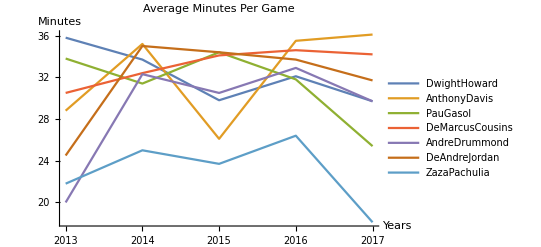

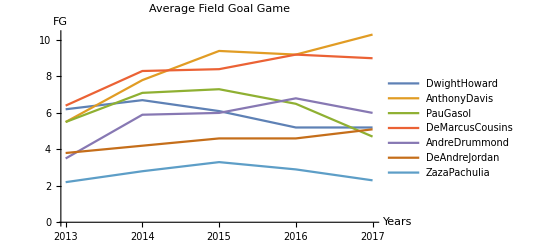

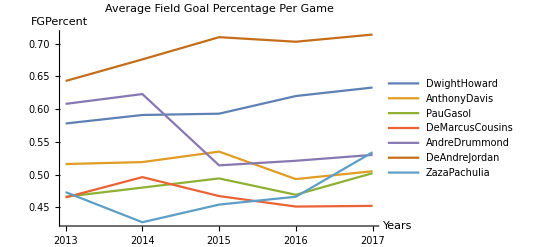

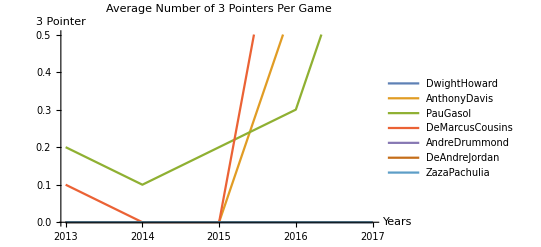

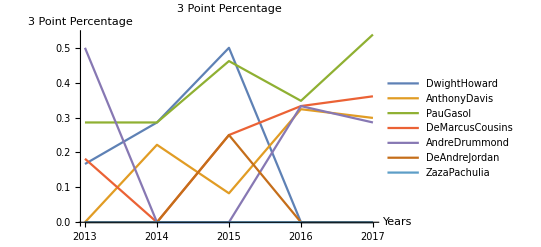

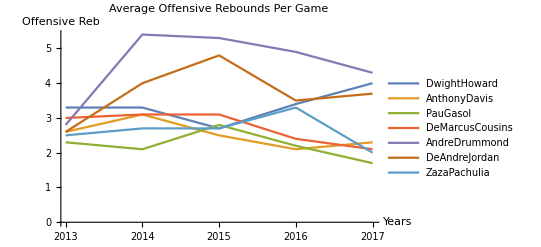

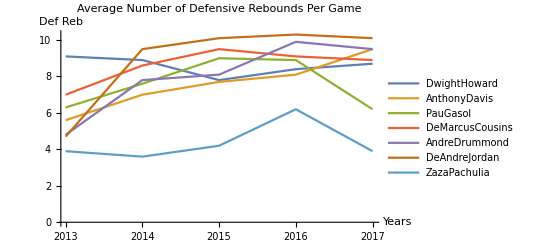

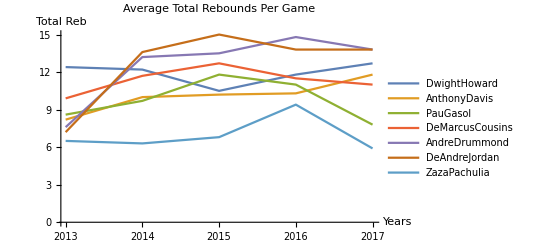

```mathematica
(*Do Bigs Matter In The NBA?
William Rodrigues*)


DwightHowardMinutes={35.8,33.7,29.8,32.1,29.7};
DwightHowardFG={6.2,6.7,6.1,5.2,5.2};
DwightHowardFGPercent={.578,.591,.593,.620,.633};
DwightHoward3P={0,0,0,0,0};
DwightHoward3PPercent={0.167,.286,.5,0,0};
DwightHowardOReb={3.3,3.3,2.7,3.4,4.0};
DwightHowardDReb={9.1,8.9,7.8,8.4,8.7};
DwightHowardTReb={12.4,12.2,10.5,11.8,12.7};
DwightHowardBlk={2.4,1.8,1.3,1.6,1.2};
DwightHowardPPG={17.1,18.3,15.8,13.7,13.5};

AnthonyDavisMinutes={28.8,35.2,26.1,35.5,36.1};
AnthonyDavisFG={5.5,7.8,9.4,9.2,10.3};
AnthonyDavisFGPercent={.516,.519,.535,.493,.505};
AnthonyDavis3P={0,0,0,.6,.5};
AnthonyDavis3PPercent={.0,.222,.083,.324,.299};
AnthonyDavisOReb={2.6,3.1,2.5,2.1,2.3};
AnthonyDavisDReb={5.6,7.0,7.7,8.1,9.5};
AnthonyDavisTReb={8.2,10.0,10.2,10.3,11.8};
AnthonyDavisBlk={1.8,2.8,2.9,2.0,2.2};
AnthonyDavisPPG={13.5,20.8,24.4,24.3,28.0,25.2};

PauGasolMinutes={33.8,31.4,34.4,31.8,25.4};
PauGasolFG={5.5,7.1,7.3,6.5,4.7};
PauGasolFGPercent={.466,.480,.494,.469,.502};
PauGasol3P={.2,.1,.2,.3,.9};
PauGasol3PPercent={.286,.286,.462,.348,.538};
PauGasolOReb={2.3,2.1,2.8,2.2,1.7};
PauGasolDReb={6.3,7.6,9.0,8.9,6.2};
PauGasolTReb={8.6,9.7,11.8,11,7.8};
PauGasolBlk={1.2,1.5,1.9,2.0,1.1};
PauGasolPPG={13.7,17.4,18.5,16.5,12.4};

DeMarcusCousinsMinutes={30.5,32.4,34.1,34.6,34.2};
DeMarcusCousinsFG={6.4,8.3,8.4,9.2,9.0};
DeMarcusCousinsFGPercent={.465,.496,.467,.451,.452};
DeMarcusCousins3P={.1,.0,.0,1.1,1.8};
DeMarcusCousins3PPercent={.182,.0,.250,.333,.361};
DeMarcusCousinsOReb={3,3.1,3.1,2.4,2.1};
DeMarcusCousinsDReb={7,8.6,9.5,9.1,8.9};
DeMarcusCousinsTReb={9.9,11.7,12.7,11.5,11};
DeMarcusCousinsBlk={.7,1.3,1.7,1.4,1.3};
DeMarcusCousinsPPG={17.1,22.7,24.1,26.9,27};


AndreDrummondMinutes={20,32.3,30.5,32.9,29.7};
AndreDrummondFG={3.5,5.9,6.0,6.8,6.0};
AndreDrummondFGPercent={.608,.623,.514,.521,.530};
AndreDrummond3P={0,0,0,0,0};
AndreDrummond3PPercent={.5,0,0,.333,.286};
AndreDrummondOReb={2.8,5.4,5.3,4.9,4.3};
AndreDrummondDReb={4.8,7.8,8.1,9.9,9.5};
AndreDrummondTReb={7.6,13.2,13.5,14.8,13.8};
AndreDrummondBlk={1.6,1.6,1.9,1.4,1.1};
AndreDrummondPPG={7.9,13.5,13.8,16.2,13.6};

DeAndreJordanMinutes={24.5,35,34.4,33.7,31.7};
DeAndreJordanFG={3.8,4.2,4.6,4.6,5.1};
DeAndreJordanFGPercent={.643,.676,.710,.703,.714};
DeAndreJordan3P={0,0,0,0,0};
DeAndreJordan3PPercent={0,0,.25,0,0};
DeAndreJordanOReb={2.6,4.0,4.8,3.5,3.7};
DeAndreJordanDReb={4.7,9.5,10.1,10.3,10.1};
DeAndreJordanTReb={7.2,13.6,15,13.8,13.8};
DeAndreJordanBlk={1.4,2.5,2.2,2.3,1.7};
DeAndreJordanPPG={8.8,10.4,11.5,12.7,12.7};

ZazaPachuliaMinutes={21.8,25,23.7,26.4,18.1};
ZazaPachuliaFG={2.2,2.8,3.3,2.9,2.3};
ZazaPachuliaFGPercent={.473,.427,.454,.466,.534};
ZazaPachulia3P={0,0,0,0,0};
ZazaPachulia3PPercent={0,0,0,0,0};
ZazaPachuliaOReb={2.5,2.7,2.7,3.3,2.0};
ZazaPachuliaDReb={3.9,3.6,4.2,6.2,3.9};
ZazaPachuliaTReb={6.5,6.3,6.8,9.4,5.9};
ZazaPachuliaBlk={.2,.3,.3,.3,.5};
ZazaPachuliaPPG={5.9,7.7,8.3,8.6,6.1};

years={2013,2014,2015,2016,2017};
players={"DwightHoward","AnthonyDavis","PauGasol","DeMarcusCousins","AndreDrummond", "DeAndreJordan","ZazaPachulia"};

ListLinePlot[{DwightHowardMinutes,AnthonyDavisMinutes,PauGasolMinutes,DeMarcusCousinsMinutes,AndreDrummondMinutes,DeAndreJordanMinutes,ZazaPachuliaMinutes},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Minutes Per Game"]

ListLinePlot[{DwightHowardFG,AnthonyDavisFG,PauGasolFG,DeMarcusCousinsFG,AndreDrummondFG,DeAndreJordanFG,ZazaPachuliaFG},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","FG"},PlotLabel->"Average Field Goal Game"]

ListLinePlot[{DwightHowardFGPercent,AnthonyDavisFGPercent,PauGasolFGPercent,DeMarcusCousinsFGPercent,AndreDrummondFGPercent,DeAndreJordanFGPercent,ZazaPachuliaFGPercent},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","FGPercent"},PlotLabel->"Average Field Goal Percentage Per Game"]

ListLinePlot[{DwightHoward3P,AnthonyDavis3P,PauGasol3P,DeMarcusCousins3P,AndreDrummond3P,DeAndreJordan3P,ZazaPachulia3P},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","3 Pointer"},PlotLabel->"Average Number of 3 Pointers Per Game"]

ListLinePlot[{DwightHoward3PPercent,AnthonyDavis3PPercent,PauGasol3PPercent,DeMarcusCousins3PPercent,AndreDrummond3PPercent,DeAndreJordan3PPercent,ZazaPachulia3PPercent},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","3 Point Percentage"},PlotLabel->" 3 Point Percentage"]

ListLinePlot[{DwightHowardOReb,AnthonyDavisOReb,PauGasolOReb,DeMarcusCousinsOReb,AndreDrummondOReb,DeAndreJordanOReb,ZazaPachuliaOReb},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","Offensive Reb"},PlotLabel->"Average Offensive Rebounds Per Game"]

ListLinePlot[{DwightHowardDReb,AnthonyDavisDReb,PauGasolDReb,DeMarcusCousinsDReb,AndreDrummondDReb,DeAndreJordanDReb,ZazaPachuliaDReb},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","Def Reb"},PlotLabel->"Average Number of Defensive Rebounds Per Game"]

ListLinePlot[{DwightHowardTReb,AnthonyDavisTReb,PauGasolTReb,DeMarcusCousinsTReb,AndreDrummondTReb,DeAndreJordanTReb,ZazaPachuliaTReb},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","Total Reb"},PlotLabel->"Average Total Rebounds Per Game"]

ListLinePlot[{DwightHowardBlk,AnthonyDavisBlk,PauGasolBlk,DeMarcusCousinsBlk,AndreDrummondBlk,DeAndreJordanBlk,ZazaPachuliaBlk},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","Blocks"},PlotLabel->"Average Number of Blocks Per Game"]

ListLinePlot[{DwightHowardPPG,AnthonyDavisPPG,PauGasolPPG,DeMarcusCousinsPPG,AndreDrummondPPG,DeAndreJordanPPG,ZazaPachuliaPPG},DataRange->{years[[1]],years[[-1]]} , PlotLegends->{players[[1]],players[[2]],players[[3]],players[[4]],players[[5]],players[[6]],players[[7]]},AxesLabel->{"Years","PPG"},PlotLabel->"Average Number of Points Per Game"]
```

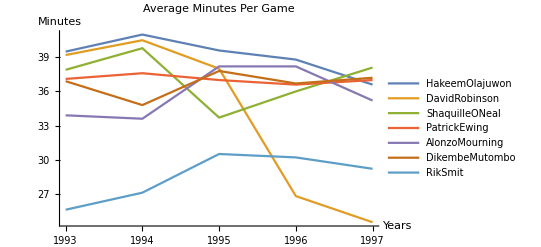

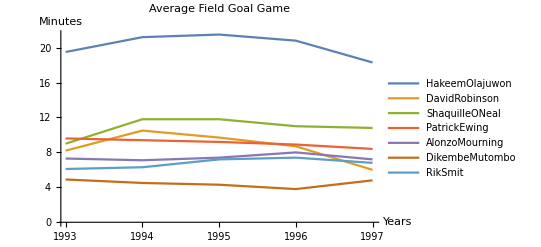

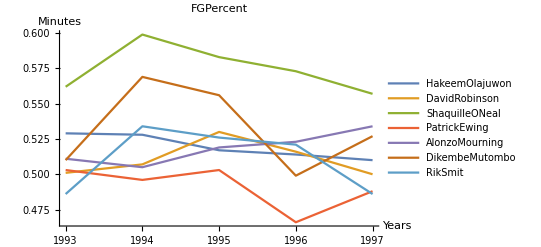

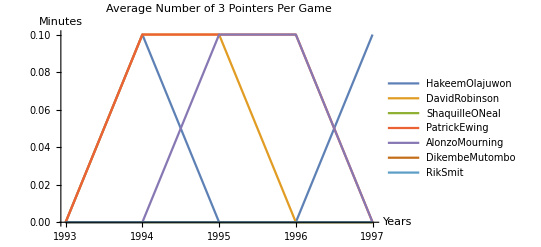

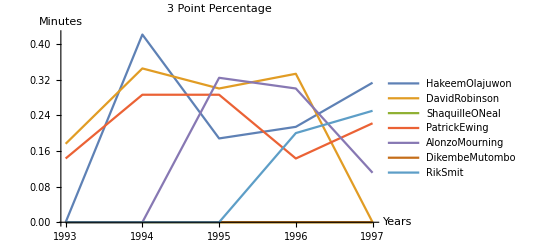

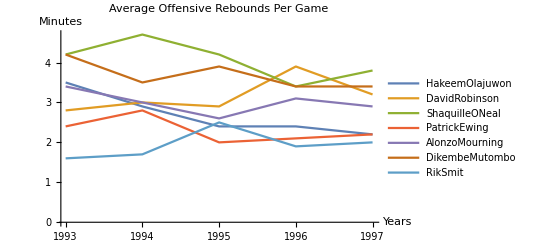

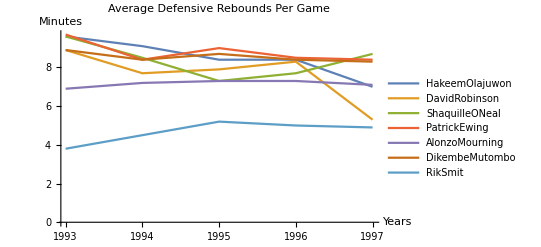

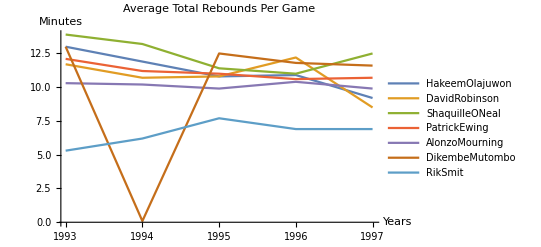

```mathematica
HakeemOlajuwonMinutes={39.5,41,39.6,38.8,36.6};
HakeemOlajuwonFG={19.5,21.2,21.5,20.8,18.3};
HakeemOlajuwonFGPercent={.529,.528,.517,.514,.510};
HakeemOlajuwon3P={0,.1,0,0,.1};
HakeemOlajuwon3PPercent={0,.421,.188,.214,.313};
HakeemOlajuwonOReb={3.5,2.9,2.4,2.4,2.2};
HakeemOlajuwonDReb={9.6,9.1,8.4,8.4,7};
HakeemOlajuwonTReb={13,11.9,10.8,10.9,9.2};
HakeemOlajuwonBlk={4.2,3.7,3.4,2.9,2.2};
HakeemOlajuwonPPG={26.1,27.3,27.8,26.9,23.2};

DavidRobinsonMinutes={39.2,40.5,38,26.8,24.5};
DavidRobinsonFG={8.2,10.5,9.7,8.7,6};
DavidRobinsonFGPercent={.501,.507,.530,.516,.5};
DavidRobinson3P={0,.1,.1,0,0};
DavidRobinson3PPercent={.176,.345,.3,.333,.0};
DavidRobinsonOReb={2.8,3,2.9,3.9,3.2};
DavidRobinsonDReb={8.9,7.7,7.9,8.3,5.3};
DavidRobinsonTReb={11.7,10.7,10.8,12.2,8.5};
DavidRobinsonBlk={3.2,3.3,3.2,3.3,1};
DavidRobinsonPPG={23.4,29.8,27.6,25,17.7};

ShaquilleONealMinutes={37.9,39.8,33.7,36,38.1};
ShaquilleONealFG={9,11.8,11.8,11,10.8};
ShaquilleONealFGPercent={.562,.599,.583,.573,.557};
ShaquilleONeal3P={0,0,0,0,0};
ShaquilleONeal3PPercent={0,0,0,0,0};
ShaquilleONealOReb={4.2,4.7,4.2,3.4,3.8};
ShaquilleONealDReb={9.6,8.5,7.3,7.7,8.7};
ShaquilleONealTReb={13.9,13.2,11.4,11,12.5};
ShaquilleONealBlk={3.5,2.9,2.4,2.1,2.9};
ShaquilleONealPPG={23.4,29.3,29.3,26.6,26.2};

PatrickEwingMinutes={37.1,37.6,37,36.6,37};
PatrickEwingFG={9.6,9.4,9.2,8.9,8.4};
PatrickEwingFGPercent={.503,.496,.503,.466,.488};
PatrickEwing3P={0,.1,.1,.1,0};
PatrickEwing3PPercent={.143,.286,.286,.143,.222};
PatrickEwingOReb={2.4,2.8,2,2.1,2.2};
PatrickEwingDReb={9.7,8.4,9,8.5,8.4};
PatrickEwingTReb={12.1,11.2,11,10.6,10.7};
PatrickEwingBlk={2,2.7,2,2.4,2.4};
PatrickEwingPPG={24.1,24.5,23.9,22.5,22.4};

AlonzoMourningMinutes={33.9,33.6,38.2,38.2,35.2};
AlonzoMourningFG={7.3,7.1,7.4,8,7.2};
AlonzoMourningFGPercent={.511,.505,.519,.523,.534};
AlonzoMourning3P={0,0,.1,.1,0};
AlonzoMourning3PPercent={0,0,.324,.3,.111};
AlonzoMourningOReb={3.4,3,2.6,3.1,2.9};
AlonzoMourningDReb={6.9,7.2,7.3,7.3,7.1};
AlonzoMourningTReb={10.3,10.2,9.9,10.4,9.9};
AlonzoMourningBlk={3.5,3.1,2.9,2.7,2.9};
AlonzoMourningPPG={21,21.5,21.3,23.2,19.8};

DikembeMutomboMinutes={36.9,34.8,37.8,36.7,37.2};
DikembeMutomboFG={4.9,4.5,4.3,3.8,4.8};
DikembeMutomboFGPercent={.510,.569,.556,.499,.527};
DikembeMutombo3P={0,0,0,0,0};
DikembeMutombo3PPercent={0,0,0,0,0};
DikembeMutomboOReb={4.2,3.5,3.9,3.4,3.4};
DikembeMutomboDReb={8.9,8.4,8.7,8.4,8.3};
DikembeMutomboTReb={13,.11.8,12.5,11.8,11.6};
DikembeMutomboBlk={3.5,4.1,3.9,4.5,3.3};
DikembeMutomboPPG={13.8,12,11.5,11,13.3};

RikSmitMinutes={25.6,27.1,30.5,30.2,29.2};
RikSmitFG={6.1,6.3,7.2,7.4,6.8};
RikSmitFGPercent={.486,.534,.526,.521,.486};
RikSmit3P={0,0,0,0,0};
RikSmit3PPercent={0,0,0,.2,.25};
RikSmitOReb={1.6,1.7,2.5,1.9,2};
RikSmitDReb={3.8,4.5,5.2,5,4.9};
RikSmitTReb={5.3,6.2,7.7,6.9,6.9};
RikSmitBlk={.9,1.1,1,.7,1.1};
RikSmitPPG={14.3,15.7,17.9,18.5};

year={1993,1994,1995,1996,1997};
player={"HakeemOlajuwon","DavidRobinson","ShaquilleONeal","PatrickEwing","AlonzoMourning","DikembeMutombo","RikSmit"};
stat={"Minutes","FG","FGPercent","3P","3PPercent","OReb","DReb","TReb",
"Blk","PPG"};

ListLinePlot[{HakeemOlajuwonMinutes,DavidRobinsonMinutes,ShaquilleONealMinutes,PatrickEwingMinutes,AlonzoMourningMinutes,DikembeMutomboMinutes,RikSmitMinutes},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Minutes Per Game"]

ListLinePlot[{HakeemOlajuwonFG,DavidRobinsonFG,ShaquilleONealFG,PatrickEwingFG,AlonzoMourningFG,DikembeMutomboFG,RikSmitFG},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Field Goal Game"]

ListLinePlot[{HakeemOlajuwonFGPercent,DavidRobinsonFGPercent,ShaquilleONealFGPercent,PatrickEwingFGPercent,AlonzoMourningFGPercent,DikembeMutomboFGPercent,RikSmitFGPercent},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"FGPercent"]

ListLinePlot[{HakeemOlajuwon3P,DavidRobinson3P,ShaquilleONeal3P,PatrickEwing3P,AlonzoMourning3P,DikembeMutombo3P,RikSmit3P},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Number of 3 Pointers Per Game"]

ListLinePlot[{HakeemOlajuwon3PPercent,DavidRobinson3PPercent,ShaquilleONeal3PPercent,PatrickEwing3PPercent,AlonzoMourning3PPercent,DikembeMutombo3PPercent,RikSmit3PPercent},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"3 Point Percentage"]

ListLinePlot[{HakeemOlajuwonOReb,DavidRobinsonOReb,ShaquilleONealOReb,PatrickEwingOReb,AlonzoMourningOReb,DikembeMutomboOReb,RikSmitOReb},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Offensive Rebounds Per Game"]

ListLinePlot[{HakeemOlajuwonDReb,DavidRobinsonDReb,ShaquilleONealDReb,PatrickEwingDReb,AlonzoMourningDReb,DikembeMutomboDReb,RikSmitDReb},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Defensive Rebounds Per Game"]

ListLinePlot[{HakeemOlajuwonTReb,DavidRobinsonTReb,ShaquilleONealTReb,PatrickEwingTReb,AlonzoMourningTReb,DikembeMutomboTReb,RikSmitTReb},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Total Rebounds Per Game"]

ListLinePlot[{HakeemOlajuwonBlk,DavidRobinsonBlk,ShaquilleONealBlk,PatrickEwingBlk,AlonzoMourningBlk,DikembeMutomboBlk,RikSmitBlk},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Number of Blocks Per Game"]

ListLinePlot[{HakeemOlajuwonPPG,DavidRobinsonPPG,ShaquilleONealPPG,PatrickEwingPPG,AlonzoMourningPPG,DikembeMutomboPPG,RikSmitPPG},DataRange->{year[[1]],year[[-1]]} , PlotLegends->{player[[1]],player[[2]],player[[3]],player[[4]],player[[5]],player[[6]],player[[7]]},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Number of Points Per Game"]
```

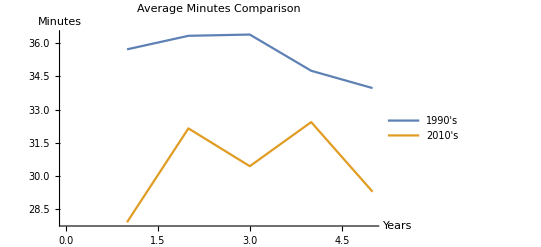

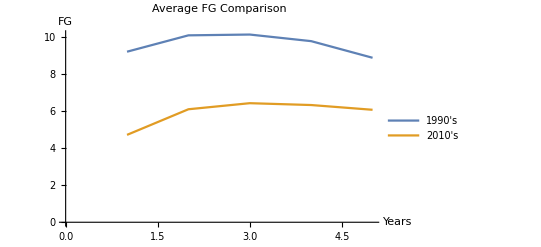

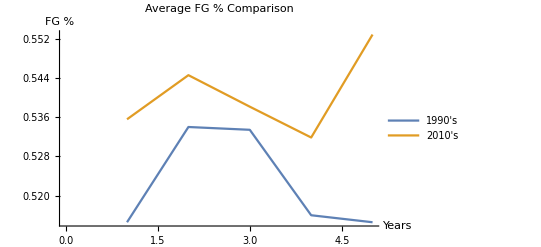

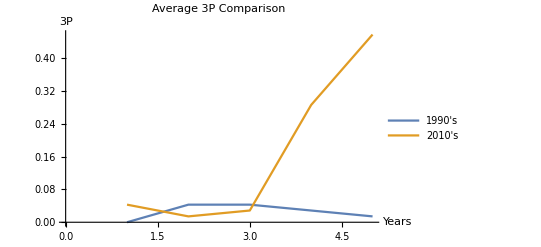

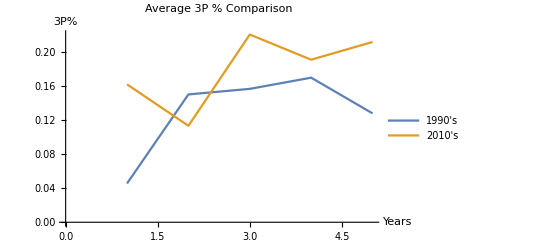

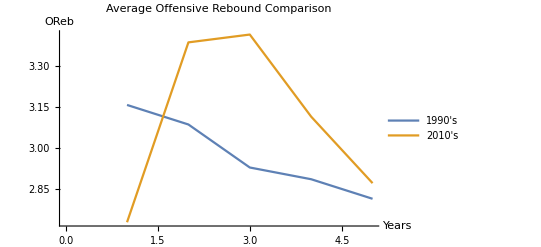

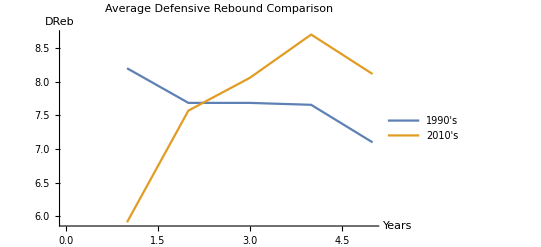

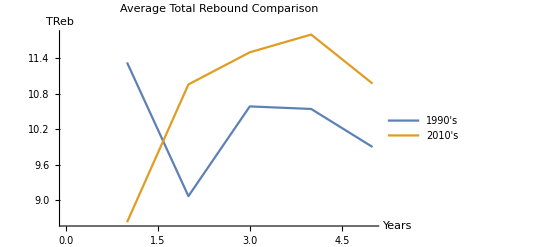

Part::partw: Part 5 of {14.3,15.7,17.9,18.5} does not exist.

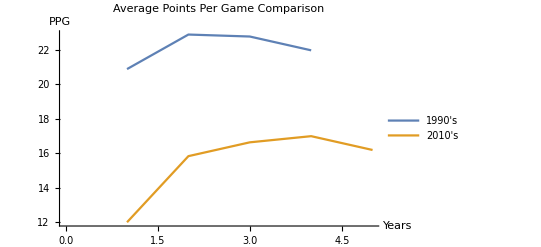

```mathematica
n=5;
AvgMinutes20={};
AvgMinutes90={};
For[i=1,i≤n,i++,
k=(DwightHowardMinutes[[i]]+AnthonyDavisMinutes[[i]]+PauGasolMinutes[[i]]+DeMarcusCousinsMinutes[[i]]+AndreDrummondMinutes[[i]]+DeAndreJordanMinutes[[i]]+ZazaPachuliaMinutes[[i]])/7;
AppendTo[AvgMinutes20,k];
t=(HakeemOlajuwonMinutes[[i]]+DavidRobinsonMinutes[[i]]+ShaquilleONealMinutes[[i]]+PatrickEwingMinutes[[i]]+AlonzoMourningMinutes[[i]]+DikembeMutomboMinutes[[i]]+RikSmitMinutes[[i]])/7;
AppendTo[AvgMinutes90,t];
]

ListLinePlot[{AvgMinutes90,AvgMinutes20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","Minutes"},PlotLabel->"Average Minutes Comparison"]

AvgFG20={};
AvgFG90={};
For[i=1,i≤n,i++,
k=(DwightHowardFG[[i]]+AnthonyDavisFG[[i]]+PauGasolFG[[i]]+DeMarcusCousinsFG[[i]]+AndreDrummondFG[[i]]+DeAndreJordanFG[[i]]+ZazaPachuliaFG[[i]])/7;
AppendTo[AvgFG20,k];
t=(HakeemOlajuwonFG[[i]]+DavidRobinsonFG[[i]]+ShaquilleONealFG[[i]]+PatrickEwingFG[[i]]+AlonzoMourningFG[[i]]+DikembeMutomboFG[[i]]+RikSmitFG[[i]])/7;
AppendTo[AvgFG90,t];
]

ListLinePlot[{AvgFG90,AvgFG20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","FG"},PlotLabel->"Average FG Comparison"]

AvgFGPercent20={};
AvgFGPercent90={};
For[i=1,i≤n,i++,
k=(DwightHowardFGPercent[[i]]+AnthonyDavisFGPercent[[i]]+PauGasolFGPercent[[i]]+DeMarcusCousinsFGPercent[[i]]+AndreDrummondFGPercent[[i]]+DeAndreJordanFGPercent[[i]]+ZazaPachuliaFGPercent[[i]])/7;
AppendTo[AvgFGPercent20,k];
t=(HakeemOlajuwonFGPercent[[i]]+DavidRobinsonFGPercent[[i]]+ShaquilleONealFGPercent[[i]]+PatrickEwingFGPercent[[i]]+AlonzoMourningFGPercent[[i]]+DikembeMutomboFGPercent[[i]]+RikSmitFGPercent[[i]])/7;
AppendTo[AvgFGPercent90,t];
]

ListLinePlot[{AvgFGPercent90,AvgFGPercent20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","FG %"},PlotLabel->"Average FG % Comparison"]

Avg3P20={};
Avg3P90={};
For[i=1,i≤n,i++,
k=(DwightHoward3P[[i]]+AnthonyDavis3P[[i]]+PauGasol3P[[i]]+DeMarcusCousins3P[[i]]+AndreDrummond3P[[i]]+DeAndreJordan3P[[i]]+ZazaPachulia3P[[i]])/7;
AppendTo[Avg3P20,k];
t=(HakeemOlajuwon3P[[i]]+DavidRobinson3P[[i]]+ShaquilleONeal3P[[i]]+PatrickEwing3P[[i]]+AlonzoMourning3P[[i]]+DikembeMutombo3P[[i]]+RikSmit3P[[i]])/7;
AppendTo[Avg3P90,t];
]

ListLinePlot[{Avg3P90,Avg3P20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","3P"},PlotLabel->"Average 3P Comparison"]

Avg3PPercent20={};
Avg3PPercent90={};
For[i=1,i≤n,i++,
k=(DwightHoward3PPercent[[i]]+AnthonyDavis3PPercent[[i]]+PauGasol3PPercent[[i]]+DeMarcusCousins3PPercent[[i]]+AndreDrummond3PPercent[[i]]+DeAndreJordan3PPercent[[i]]+ZazaPachulia3PPercent[[i]])/7;
AppendTo[Avg3PPercent20,k];
t=(HakeemOlajuwon3PPercent[[i]]+DavidRobinson3PPercent[[i]]+ShaquilleONeal3PPercent[[i]]+PatrickEwing3PPercent[[i]]+AlonzoMourning3PPercent[[i]]+DikembeMutombo3PPercent[[i]]+RikSmit3PPercent[[i]])/7;
AppendTo[Avg3PPercent90,t];
]

ListLinePlot[{Avg3PPercent90,Avg3PPercent20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","3P%"},PlotLabel->"Average 3P % Comparison"]

AvgOReb20={};
AvgOReb90={};
For[i=1,i≤n,i++,
k=(DwightHowardOReb[[i]]+AnthonyDavisOReb[[i]]+PauGasolOReb[[i]]+DeMarcusCousinsOReb[[i]]+AndreDrummondOReb[[i]]+DeAndreJordanOReb[[i]]+ZazaPachuliaOReb[[i]])/7;
AppendTo[AvgOReb20,k];
t=(HakeemOlajuwonOReb[[i]]+DavidRobinsonOReb[[i]]+ShaquilleONealOReb[[i]]+PatrickEwingOReb[[i]]+AlonzoMourningOReb[[i]]+DikembeMutomboOReb[[i]]+RikSmitOReb[[i]])/7;
AppendTo[AvgOReb90,t];
]

ListLinePlot[{AvgOReb90,AvgOReb20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","OReb"},PlotLabel->"Average Offensive Rebound Comparison"]

AvgDReb20={};
AvgDReb90={};
For[i=1,i≤n,i++,
k=(DwightHowardDReb[[i]]+AnthonyDavisDReb[[i]]+PauGasolDReb[[i]]+DeMarcusCousinsDReb[[i]]+AndreDrummondDReb[[i]]+DeAndreJordanDReb[[i]]+ZazaPachuliaDReb[[i]])/7;
AppendTo[AvgDReb20,k];
t=(HakeemOlajuwonDReb[[i]]+DavidRobinsonDReb[[i]]+ShaquilleONealDReb[[i]]+PatrickEwingDReb[[i]]+AlonzoMourningDReb[[i]]+DikembeMutomboDReb[[i]]+RikSmitDReb[[i]])/7;
AppendTo[AvgDReb90,t];
]

ListLinePlot[{AvgDReb90,AvgDReb20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","DReb"},PlotLabel->"Average Defensive Rebound Comparison"]

AvgTReb20={};
AvgTReb90={};
For[i=1,i≤n,i++,
k=(DwightHowardTReb[[i]]+AnthonyDavisTReb[[i]]+PauGasolTReb[[i]]+DeMarcusCousinsTReb[[i]]+AndreDrummondTReb[[i]]+DeAndreJordanTReb[[i]]+ZazaPachuliaTReb[[i]])/7;
AppendTo[AvgTReb20,k];
t=(HakeemOlajuwonTReb[[i]]+DavidRobinsonTReb[[i]]+ShaquilleONealTReb[[i]]+PatrickEwingTReb[[i]]+AlonzoMourningTReb[[i]]+DikembeMutomboTReb[[i]]+RikSmitTReb[[i]])/7;
AppendTo[AvgTReb90,t];
]

ListLinePlot[{AvgTReb90,AvgTReb20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","TReb"},PlotLabel->"Average Total Rebound Comparison"]

AvgBlk20={};
AvgBlk90={};
For[i=1,i≤n,i++,
k=(DwightHowardBlk[[i]]+AnthonyDavisBlk[[i]]+PauGasolBlk[[i]]+DeMarcusCousinsBlk[[i]]+AndreDrummondBlk[[i]]+DeAndreJordanBlk[[i]]+ZazaPachuliaBlk[[i]])/7;
AppendTo[AvgBlk20,k];
t=(HakeemOlajuwonBlk[[i]]+DavidRobinsonBlk[[i]]+ShaquilleONealBlk[[i]]+PatrickEwingBlk[[i]]+AlonzoMourningBlk[[i]]+DikembeMutomboBlk[[i]]+RikSmitBlk[[i]])/7;
AppendTo[AvgBlk90,t];
]

ListLinePlot[{AvgBlk90,AvgBlk20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","Block"},PlotLabel->"Average Block Comparison"]

AvgPPG20={};
AvgPPG90={};
For[i=1,i≤n,i++,
k=(DwightHowardPPG[[i]]+AnthonyDavisPPG[[i]]+PauGasolPPG[[i]]+DeMarcusCousinsPPG[[i]]+AndreDrummondPPG[[i]]+DeAndreJordanPPG[[i]]+ZazaPachuliaPPG[[i]])/7;
AppendTo[AvgPPG20,k];
t=(HakeemOlajuwonPPG[[i]]+DavidRobinsonPPG[[i]]+ShaquilleONealPPG[[i]]+PatrickEwingPPG[[i]]+AlonzoMourningPPG[[i]]+DikembeMutomboPPG[[i]]+RikSmitPPG[[i]])/7;
AppendTo[AvgPPG90,t];
]

ListLinePlot[{AvgPPG90,AvgPPG20}, PlotLegends->{"1990's","2010's"},AxesLabel->{"Years","PPG"},PlotLabel->"Average Points Per Game Comparison"]
```